May 20 2011

```mathematica
δ[n_]:=DiscreteDelta[n];
```

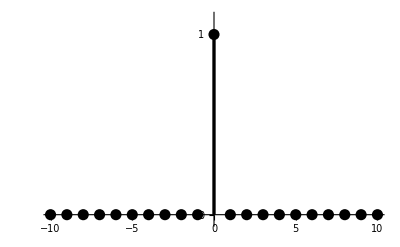

```mathematica
ListPlot[
Table[
{n,δ[n]},
{n,-10,10}
],
PlotRange->{-0.04,1.1},
Ticks->{Automatic,{0,1}},
Filling->Axis,
FillingStyle->Directive[Black, Thickness[0.006]],
PlotStyle->Directive[Black,PointSize[0.02]]
]
```

```mathematica
h[n_,N_]:=1/N∑_(k=0)^(N-1) δ[n-k]
```

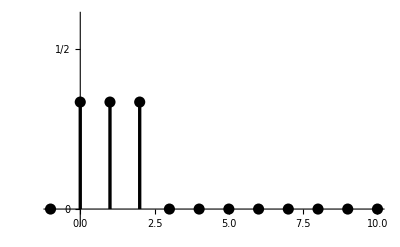

```mathematica
ListPlot[
Table[
{n,h[n,3]},
{n,-1,10}
],
PlotRange->{-0.04,0.6},
Ticks->{Automatic,{0,1/2}},
Filling->Axis,
FillingStyle->Directive[Black, Thickness[0.006]],
PlotStyle->Directive[Black,PointSize[0.02]]
]
```

```mathematica
H[z_,N_]:=∑_(n=-∞)^∞ h[n,N] z^-n
```

```mathematica
H[z,3]
```

(1+z+z^2)/(3 z^2)

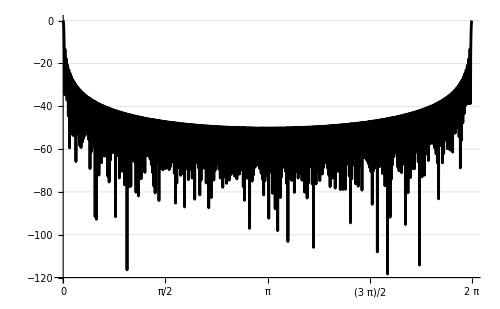

```mathematica
Plot[Evaluate[
20 Log[10,Abs[H[ⅇ^(ⅉ θ),320]]]
],
{θ,0,2π},
PlotRange->{-120,0},
AxesOrigin->{0,-120},
Ticks->{Table[i π/4,{i,0,8}],Automatic},
GridLines-> {None,Automatic},
GridLinesStyle->Directive[RGBColor[0.7,0.7,0.7]],
PlotStyle-> Directive[Black,Thickness[0.004]],
ImageSize->500
]
```

```mathematica
Manipulate[Plot[Evaluate[
20 Log[10,Abs[H[ⅇ^(ⅉ θ),N]]]
],
{θ,0,π},
PlotRange->{-120,0},
AxesOrigin->{0,-120},
Ticks->{Table[i π/4,{i,0,8}],Automatic},
TicksStyle->{{Large,Bold},{Medium, Bold}},
GridLines-> {Table[i π/4,{i,0,8}],Automatic},
GridLinesStyle->Directive[RGBColor[0.7,0.7,0.7],Dashed],
PlotLabel->Style["N="<>ToString[N],Large],
PlotStyle-> Directive[Black,Thickness[0.004]],
ImageSize->500
],
{{N,2},1,50,1}
]
```

```mathematica
Off[Refine::timc]
TableForm[Table[H[ⅇ^(ⅉ θ),N],{N,1,10}]]
```

1
1/2 ⅇ^(-ⅈ θ) (1+ⅇ^(ⅈ θ))
1/3 ⅇ^(-2 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ))
1/4 ⅇ^(-3 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ))
1/5 ⅇ^(-4 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ))
1/6 ⅇ^(-5 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)+ⅇ^(5 ⅈ θ))
1/7 ⅇ^(-6 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)+ⅇ^(5 ⅈ θ)+ⅇ^(6 ⅈ θ))
1/8 ⅇ^(-7 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)+ⅇ^(5 ⅈ θ)+ⅇ^(6 ⅈ θ)+ⅇ^(7 ⅈ θ))
1/9 ⅇ^(-8 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)+ⅇ^(5 ⅈ θ)+ⅇ^(6 ⅈ θ)+ⅇ^(7 ⅈ θ)+ⅇ^(8 ⅈ θ))
1/10 ⅇ^(-9 ⅈ θ) (1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)+ⅇ^(5 ⅈ θ)+ⅇ^(6 ⅈ θ)+ⅇ^(7 ⅈ θ)+ⅇ^(8 ⅈ θ)+ⅇ^(9 ⅈ θ))

```mathematica
Simplify[Abs[H[ⅇ^(ⅉ θ),N]],{θ∈Reals,N∈Integers, N>1}]
```

Abs[(1-ⅇ^(-ⅈ N θ))/(N-ⅇ^(ⅈ θ) N)]

```mathematica
Table[FullSimplify[H[ⅇ^(ⅉ θ),N] H[ⅇ^(ⅉ θ),N]*,{θ∈Reals,N∈Integers,N>1}],{N,2,5}]
```

{1/4 ⅇ^(2 Im[θ]) Abs[1+ⅇ^(ⅈ θ)]^2,1/9 ⅇ^(4 Im[θ]) Abs[1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)]^2,1/16 ⅇ^(6 Im[θ]) Abs[1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)]^2,1/25 ⅇ^(8 Im[θ]) Abs[1+ⅇ^(ⅈ θ)+ⅇ^(2 ⅈ θ)+ⅇ^(3 ⅈ θ)+ⅇ^(4 ⅈ θ)]^2}

```mathematica
TableForm[FullSimplify[Table[{N,H[ⅇ^(ⅉ θ),N] H[ⅇ^(ⅉ θ),N]*},{N,1,10}],{θ∈Reals}]]
```

1 | 1
2 | Cos[θ/2]^2
3 | 1/9 (1+2 Cos[θ])^2
4 | Cos[θ/2]^2 Cos[θ]^2
5 | 1/25 (1+2 Cos[θ]+2 Cos[2 θ])^2
6 | 1/9 (Cos[θ/2]+Cos[(3 θ)/2]+Cos[(5 θ)/2])^2
7 | 1/49 (1+2 Cos[θ]+2 Cos[2 θ]+2 Cos[3 θ])^2
8 | 1/16 (Cos[θ/2]+Cos[(3 θ)/2]+Cos[(5 θ)/2]+Cos[(7 θ)/2])^2
9 | 1/81 (1+2 Cos[θ]+2 Cos[2 θ]+2 Cos[3 θ]+2 Cos[4 θ])^2
10 | 1/25 (Cos[θ/2]+Cos[(3 θ)/2]+Cos[(5 θ)/2]+Cos[(7 θ)/2]+Cos[(9 θ)/2])^2